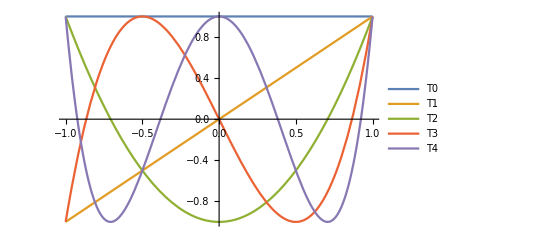

```mathematica
Plot[Evaluate[Table[ChebyshevT[n,x],{n,0,4}]],{x,-1,1},PlotLegends->Table["T"<>ToString[n],{n,0,4}],PlotRange->{{-1,1},Automatic}]
```

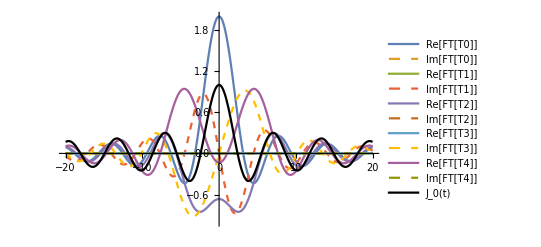

```mathematica
(*Calculate Fourier Transforms without 2π factor*)fourierTransforms=Table[Integrate[ChebyshevT[n,x] Exp[-I f x],{x,-1,1}],{n,0,4}];

(*Plot Fourier Transforms*)
plot1=Plot[Evaluate[ReIm[fourierTransforms]/.{f->freq}],{freq,-20,20},PlotRange->{{-20,20},{-1,2}},PlotStyle->{Automatic,Dashed},PlotLegends->Flatten[Table[{"Re[FT[T"<>ToString[n]<>"]]","Im[FT[T"<>ToString[n]<>"]]"},{n,0,4}]]];

(*Plot Bessel Function*)
plot2=Plot[BesselJ[0,freq],{freq,-20,20},PlotRange->{{-20,20},{-1,2}},PlotStyle->{Thick,Black},PlotLegends->{"J_0(t)"}];

(*Combine Plots and Legends*)
Show[plot1,plot2]
```